```mathematica
ClearAll["Global`*"]
```

```mathematica
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
M1[n_,k_,s_]:=Sum[ (-1)^(j+1) j^(-s)M1[n/j,k-1,s],{j,1,n}];M1[n_,0,s_]:=UnitStep[n-1]
M2[n_,k_,s_]:=Sum[ (-1)^(j+1) j^(-s)M2[n/j,k-1,s],{j,2,n}];M2[n_,0,s_]:=UnitStep[n-1]

E2a[n_,k_, a_,s_]:= E2a[n,k,a,s]=Sum[ j^(-s)E2a[n/j,k-1,a,s],{j,2,n}]-a Sum[ (j a)^(-s)E2a[n/(a j),k-1,a,s],{j,1,n/a}];E2a[n_,0,a_,s_]:=UnitStep[n-1]
E1a[n_,k_, a_,s_]:= E1a[n,k,a,s]=Sum[j^(-s) E1a[n/j,k-1,a,s],{j,1,n}]-a Sum[(j a)^(-s) E1a[n/(a j),k-1,a,s],{j,1,n/a}];E1a[n_,0,a_,s_]:=UnitStep[n-1]

DDa[n_,k_,s_]:=DDa[n,k,s]=Sum[j^(-s) DDa[Floor[n/j],k-1,s],{j,1,n}];DDa[n_,0,s_]:=UnitStep[n-1]
D2a[n_,k_,s_]:=D2a[n,k,s]=Sum[j^(-s)D2a[Floor[n/j],k-1,s],{j,2,n}];D2a[n_,0,s_]:=UnitStep[n-1]

D2b[n_,k_,s_]:=Sum[(-1)^j Binomial[k,j] DDa[n,k-j,s],{j,0,k}]
DDb[n_,k_,s_]:=Sum[Binomial[k,j] D2a[n,k-j,s],{j,0,k}]
E2b[n_,k_,b_,s_]:=Sum[(-1)^j Binomial[k,j] E1a[n,k-j,b,s],{j,0,k}]
E1b[n_,z_,b_,s_]:=Sum[ bin[z,k] E2a[n,k,b,s],{k,0,If[ b < 2, Log[b,n],Log[2,n]]}]
DDc[n_,k_,b_,s_]:=Sum[Binomial[k+j-1,k-1] b^(j(1-s)) E1a[n/(b^j), k, b,s],{j,0,Log[b,n]}]

E1c[n_,k_,b_,s_]:=Sum[(-1)^j Binomial[k,j] b^(j(1-s))  DDa[n/b^j,k,s],{j,0,k}]
E2c[n_,k_,b_,s_]:=Sum[(-1)^j b^(j(1-s)) Binomial[k,j] Binomial[j,m]D2a[n/b^j,k-m,s],{j,0,k},{m,0,j}]
D2E2[n_,k_,b_,s_]:= Sum[ (-1)^j b^(j(1-s)) Binomial[k,j] Sum[ Binomial[j,m] If[n/b^j<1,0,D2a[n/b^j,k-m,s]],{m,0,j}],{j,0,k}]
E2D2[n_,k_,b_,s_]:= (-1)^k+Sum[b^(a(1-s))/((k-1)!) Binomial[k,j]Pochhammer[a-k+j+1,k-1]E2a[b^-a n,j,b,s],{a,0,Log[b,n]},{j,0,k}]

Lin[n_,s_]:=Sum[ (-1)^(k+1)/k D2a[n,k,s],{k,Log[2,n]}]
LinE[n_,b_,s_]:=Sum[ (-1)^(k+1)/k E2a[n,k,b,s],{k,Log[2,n]}]
```

```mathematica
{E1a[100,4,3,-1], E1c[100,4,3,-1]}
```

{3761,3761}

```mathematica
{E2a[100,3,3,2], E2c[100,3,3,2],D2E2[100,3,3,2]}
```

{1559137560828081735079/1517098224317626798848000,1559137560828081735079/1517098224317626798848000,1559137560828081735079/1517098224317626798848000}

```mathematica
{E2D2[100,4,4,2], D2a[100,4,2]}
```

{383724634331/7113173760000,383724634331/7113173760000}

```mathematica
{Lin[100,-1],LinE[100,2,-1],Lin[100,-1]-LinE[100,2,-1]}
```

{69389/60,10301/60,4924/5}

```mathematica
{Lin[100,1],LinE[100,2,1],Lin[100,1]-LinE[100,2,1]}
```

{292149953504274361788974787095433526022627/139440750459424954329067617870624607113600,-49479885121316776317240876687596761405693/139440750459424954329067617870624607113600,49/20}

```mathematica
ll[n_,b_,s_]:=Lin[n,s]-LinE[n,b,s]-(Lin[n-1,s]-LinE[n-1,b,s])
ss[n_,b_,s_]:=If[ Log[b,n]==Floor[Log[b,n]],(n^(1-s))/Log[b,n],0]
Table[{n,ll[n,cc=3,-2],ll[n,cc,0],ll[n,cc,2], ss[n,cc,-2],ss[n,cc,0],ss[n,cc,2]},{n,2,100}]//TableForm
```

2 | 0 | 0 | 0 | 0 | 0 | 0
3 | 27 | 3 | 1/3 | 27 | 3 | 1/3
4 | 0 | 0 | 0 | 0 | 0 | 0
5 | 0 | 0 | 0 | 0 | 0 | 0
6 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 0 | 0 | 0 | 0 | 0
8 | 0 | 0 | 0 | 0 | 0 | 0
9 | 729/2 | 9/2 | 1/18 | 729/2 | 9/2 | 1/18
10 | 0 | 0 | 0 | 0 | 0 | 0
11 | 0 | 0 | 0 | 0 | 0 | 0
12 | 0 | 0 | 0 | 0 | 0 | 0
13 | 0 | 0 | 0 | 0 | 0 | 0
14 | 0 | 0 | 0 | 0 | 0 | 0
15 | 0 | 0 | 0 | 0 | 0 | 0
16 | 0 | 0 | 0 | 0 | 0 | 0
17 | 0 | 0 | 0 | 0 | 0 | 0
18 | 0 | 0 | 0 | 0 | 0 | 0
19 | 0 | 0 | 0 | 0 | 0 | 0
20 | 0 | 0 | 0 | 0 | 0 | 0
21 | 0 | 0 | 0 | 0 | 0 | 0
22 | 0 | 0 | 0 | 0 | 0 | 0
23 | 0 | 0 | 0 | 0 | 0 | 0
24 | 0 | 0 | 0 | 0 | 0 | 0
25 | 0 | 0 | 0 | 0 | 0 | 0
26 | 0 | 0 | 0 | 0 | 0 | 0
27 | 6561 | 9 | 1/81 | 6561 | 9 | 1/81
28 | 0 | 0 | 0 | 0 | 0 | 0
29 | 0 | 0 | 0 | 0 | 0 | 0
30 | 0 | 0 | 0 | 0 | 0 | 0
31 | 0 | 0 | 0 | 0 | 0 | 0
32 | 0 | 0 | 0 | 0 | 0 | 0
33 | 0 | 0 | 0 | 0 | 0 | 0
34 | 0 | 0 | 0 | 0 | 0 | 0
35 | 0 | 0 | 0 | 0 | 0 | 0
36 | 0 | 0 | 0 | 0 | 0 | 0
37 | 0 | 0 | 0 | 0 | 0 | 0
38 | 0 | 0 | 0 | 0 | 0 | 0
39 | 0 | 0 | 0 | 0 | 0 | 0
40 | 0 | 0 | 0 | 0 | 0 | 0
41 | 0 | 0 | 0 | 0 | 0 | 0
42 | 0 | 0 | 0 | 0 | 0 | 0
43 | 0 | 0 | 0 | 0 | 0 | 0
44 | 0 | 0 | 0 | 0 | 0 | 0
45 | 0 | 0 | 0 | 0 | 0 | 0
46 | 0 | 0 | 0 | 0 | 0 | 0
47 | 0 | 0 | 0 | 0 | 0 | 0
48 | 0 | 0 | 0 | 0 | 0 | 0
49 | 0 | 0 | 0 | 0 | 0 | 0
50 | 0 | 0 | 0 | 0 | 0 | 0
51 | 0 | 0 | 0 | 0 | 0 | 0
52 | 0 | 0 | 0 | 0 | 0 | 0
53 | 0 | 0 | 0 | 0 | 0 | 0
54 | 0 | 0 | 0 | 0 | 0 | 0
55 | 0 | 0 | 0 | 0 | 0 | 0
56 | 0 | 0 | 0 | 0 | 0 | 0
57 | 0 | 0 | 0 | 0 | 0 | 0
58 | 0 | 0 | 0 | 0 | 0 | 0
59 | 0 | 0 | 0 | 0 | 0 | 0
60 | 0 | 0 | 0 | 0 | 0 | 0
61 | 0 | 0 | 0 | 0 | 0 | 0
62 | 0 | 0 | 0 | 0 | 0 | 0
63 | 0 | 0 | 0 | 0 | 0 | 0
64 | 0 | 0 | 0 | 0 | 0 | 0
65 | 0 | 0 | 0 | 0 | 0 | 0
66 | 0 | 0 | 0 | 0 | 0 | 0
67 | 0 | 0 | 0 | 0 | 0 | 0
68 | 0 | 0 | 0 | 0 | 0 | 0
69 | 0 | 0 | 0 | 0 | 0 | 0
70 | 0 | 0 | 0 | 0 | 0 | 0
71 | 0 | 0 | 0 | 0 | 0 | 0
72 | 0 | 0 | 0 | 0 | 0 | 0
73 | 0 | 0 | 0 | 0 | 0 | 0
74 | 0 | 0 | 0 | 0 | 0 | 0
75 | 0 | 0 | 0 | 0 | 0 | 0
76 | 0 | 0 | 0 | 0 | 0 | 0
77 | 0 | 0 | 0 | 0 | 0 | 0
78 | 0 | 0 | 0 | 0 | 0 | 0
79 | 0 | 0 | 0 | 0 | 0 | 0
80 | 0 | 0 | 0 | 0 | 0 | 0
81 | 531441/4 | 81/4 | 1/324 | 531441/4 | 81/4 | 1/324
82 | 0 | 0 | 0 | 0 | 0 | 0
83 | 0 | 0 | 0 | 0 | 0 | 0
84 | 0 | 0 | 0 | 0 | 0 | 0
85 | 0 | 0 | 0 | 0 | 0 | 0
86 | 0 | 0 | 0 | 0 | 0 | 0
87 | 0 | 0 | 0 | 0 | 0 | 0
88 | 0 | 0 | 0 | 0 | 0 | 0
89 | 0 | 0 | 0 | 0 | 0 | 0
90 | 0 | 0 | 0 | 0 | 0 | 0
91 | 0 | 0 | 0 | 0 | 0 | 0
92 | 0 | 0 | 0 | 0 | 0 | 0
93 | 0 | 0 | 0 | 0 | 0 | 0
94 | 0 | 0 | 0 | 0 | 0 | 0
95 | 0 | 0 | 0 | 0 | 0 | 0
96 | 0 | 0 | 0 | 0 | 0 | 0
97 | 0 | 0 | 0 | 0 | 0 | 0
98 | 0 | 0 | 0 | 0 | 0 | 0
99 | 0 | 0 | 0 | 0 | 0 | 0
100 | 0 | 0 | 0 | 0 | 0 | 0

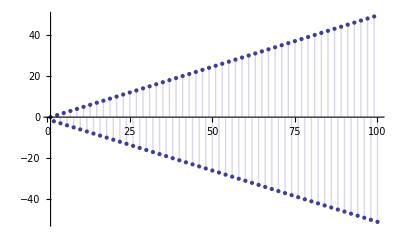

```mathematica
DiscretePlot[E2a[n,1,2,-1],{n,1,100}]
```

```mathematica
M1[100,2,-1]
```

175

```mathematica
E1a[100,2,2,-1]
```

175

```mathematica
ll[n_,b_,s_]:=Lin[n,s]-LinE[n,b,s]
ss[n_,b_,s_]:=Sum[(b^(1-s))^k/k,{k,1,Log[b,n]}]
Table[{n,ll[n,cc=3,-2],ll[n,cc,0],ll[n,cc,2], ss[n,cc,-2],ss[n,cc,0],ss[n,cc,2]},{n,2,100}]//TableForm
```

2 | 0 | 0 | 0 | 0 | 0 | 0
3 | 27 | 3 | 1/3 | 27 | 3 | 1/3
4 | 27 | 3 | 1/3 | 27 | 3 | 1/3
5 | 27 | 3 | 1/3 | 27 | 3 | 1/3
6 | 27 | 3 | 1/3 | 27 | 3 | 1/3
7 | 27 | 3 | 1/3 | 27 | 3 | 1/3
8 | 27 | 3 | 1/3 | 27 | 3 | 1/3
9 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
10 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
11 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
12 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
13 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
14 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
15 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
16 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
17 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
18 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
19 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
20 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
21 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
22 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
23 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
24 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
25 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
26 | 783/2 | 15/2 | 7/18 | 783/2 | 15/2 | 7/18
27 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
28 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
29 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
30 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
31 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
32 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
33 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
34 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
35 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
36 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
37 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
38 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
39 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
40 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
41 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
42 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
43 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
44 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
45 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
46 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
47 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
48 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
49 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
50 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
51 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
52 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
53 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
54 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
55 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
56 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
57 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
58 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
59 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
60 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
61 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
62 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
63 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
64 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
65 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
66 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
67 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
68 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
69 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
70 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
71 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
72 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
73 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
74 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
75 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
76 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
77 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
78 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
79 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
80 | 13905/2 | 33/2 | 65/162 | 13905/2 | 33/2 | 65/162
81 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
82 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
83 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
84 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
85 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
86 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
87 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
88 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
89 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
90 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
91 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
92 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
93 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
94 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
95 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
96 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
97 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
98 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
99 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324
100 | 559251/4 | 147/4 | 131/324 | 559251/4 | 147/4 | 131/324

```mathematica
fg[n_, b_, s_]:=Sum[((b^(1-s))^k-1)/k,{k,1,Log[b,n]}]
```

```mathematica
N[fg[100,1.001,0]]
```

28.0218

```mathematica
N[LogIntegral[100]-Log[Log[100]]-EulerGamma]
```

28.0217

```mathematica
N[fg[100,1.001,1]]
```

0.

```mathematica
N[fg[100,1.0001,-1]]
```

1243.45

```mathematica
N[fg[100,1.001,-2]]
```

78630.3

```mathematica
N[fg[100,1.001,2]]
```

-2.10573

```mathematica
N[fg[100,1.001,1/2+3I]]
```

-2.51851-1.57252 ⅈ

```mathematica
Table[{n,N[fg[100,1.01,1/2+n I]]},{n,-50,50,1}]//TableForm
```

-50 | -6.03848+1.36328 ⅈ
-49 | -6.0166+1.30252 ⅈ
-48 | -5.92975+1.31723 ⅈ
-47 | -5.92623+1.38897 ⅈ
-46 | -5.97071+1.3693 ⅈ
-45 | -5.91648+1.31071 ⅈ
-44 | -5.83322+1.35627 ⅈ
-43 | -5.85847+1.41913 ⅈ
-42 | -5.8885+1.36921 ⅈ
-41 | -5.80261+1.32656 ⅈ
-40 | -5.73647+1.40051 ⅈ
-39 | -5.78616+1.44064 ⅈ
-38 | -5.78758+1.3659 ⅈ
-37 | -5.6765+1.35266 ⅈ
-36 | -5.64002+1.4466 ⅈ
-35 | -5.70371+1.45156 ⅈ
-34 | -5.66423+1.36338 ⅈ
-33 | -5.54012+1.39045 ⅈ
-32 | -5.5425+1.49028 ⅈ
-31 | -5.60405+1.45134 ⅈ
-30 | -5.51538+1.36643 ⅈ
-29 | -5.3952+1.43995 ⅈ
-28 | -5.44011+1.52681 ⅈ
-27 | -5.47859+1.44106 ⅈ
-26 | -5.33833+1.38023 ⅈ
-25 | -5.24236+1.49969 ⅈ
-24 | -5.3259+1.55143 ⅈ
-23 | -5.31692+1.42343 ⅈ
-22 | -5.12988+1.41012 ⅈ
-21 | -5.07992+1.56691 ⅈ
-20 | -5.18886+1.55953 ⅈ
-19 | -5.10543+1.40279 ⅈ
-18 | -4.88449+1.46195 ⅈ
-17 | -4.90228+1.638 ⅈ
-16 | -5.01179+1.54631 ⅈ
-15 | -4.8234+1.38503 ⅈ
-14 | -4.59023+1.5439 ⅈ
-13 | -4.69743+1.70935 ⅈ
-12 | -4.76563+1.50447 ⅈ
-11 | -4.43103+1.37851 ⅈ
-10 | -4.21884+1.67405 ⅈ
-9 | -4.44241+1.77907 ⅈ
-8 | -4.39042+1.4141 ⅈ
-7 | -3.82432+1.40038 ⅈ
-6 | -3.69308+1.91871 ⅈ
-5 | -4.10098+1.85114 ⅈ
-4 | -3.69578+1.17243 ⅈ
-3 | -2.52221+1.55255 ⅈ
-2 | -2.74353+2.86457 ⅈ
-1 | -4.20165+1.71319 ⅈ
0 | 4.74572
1 | -4.20165-1.71319 ⅈ
2 | -2.74353-2.86457 ⅈ
3 | -2.52221-1.55255 ⅈ
4 | -3.69578-1.17243 ⅈ
5 | -4.10098-1.85114 ⅈ
6 | -3.69308-1.91871 ⅈ
7 | -3.82432-1.40038 ⅈ
8 | -4.39042-1.4141 ⅈ
9 | -4.44241-1.77907 ⅈ
10 | -4.21884-1.67405 ⅈ
11 | -4.43103-1.37851 ⅈ
12 | -4.76563-1.50447 ⅈ
13 | -4.69743-1.70935 ⅈ
14 | -4.59023-1.5439 ⅈ
15 | -4.8234-1.38503 ⅈ
16 | -5.01179-1.54631 ⅈ
17 | -4.90228-1.638 ⅈ
18 | -4.88449-1.46195 ⅈ
19 | -5.10543-1.40279 ⅈ
20 | -5.18886-1.55953 ⅈ
21 | -5.07992-1.56691 ⅈ
22 | -5.12988-1.41012 ⅈ
23 | -5.31692-1.42343 ⅈ
24 | -5.3259-1.55143 ⅈ
25 | -5.24236-1.49969 ⅈ
26 | -5.33833-1.38023 ⅈ
27 | -5.47859-1.44106 ⅈ
28 | -5.44011-1.52681 ⅈ
29 | -5.3952-1.43995 ⅈ
30 | -5.51538-1.36643 ⅈ
31 | -5.60405-1.45134 ⅈ
32 | -5.5425-1.49028 ⅈ
33 | -5.54012-1.39045 ⅈ
34 | -5.66423-1.36338 ⅈ
35 | -5.70371-1.45156 ⅈ
36 | -5.64002-1.4466 ⅈ
37 | -5.6765-1.35266 ⅈ
38 | -5.78758-1.3659 ⅈ
39 | -5.78616-1.44064 ⅈ
40 | -5.73647-1.40051 ⅈ
41 | -5.80261-1.32656 ⅈ
42 | -5.8885-1.36921 ⅈ
43 | -5.85847-1.41913 ⅈ
44 | -5.83322-1.35627 ⅈ
45 | -5.91648-1.31071 ⅈ
46 | -5.97071-1.3693 ⅈ
47 | -5.92623-1.38897 ⅈ
48 | -5.92975-1.31723 ⅈ
49 | -6.0166-1.30252 ⅈ
50 | -6.03848-1.36328 ⅈ

```mathematica
fga[n_, b_, s_]:=Sum[((b^(1-s))^k-1)/k,{k,1,Log[b,n]}]
```

```mathematica
Expand[fga[100,b,s]]
```

-HarmonicNumber[Log[100]/Log[b]]-(b^(1-s))^(1+Log[100]/Log[b]) LerchPhi[b^(1-s),1,1+Log[100]/Log[b]]-Log[b^-s (-b+b^s)]

```mathematica
Limit[-HarmonicNumber[Log[100]/Log[b]]-Log[b^-s (-b+b^s)],{b->1}]
```

```mathematica
{-EulerGamma-Log[(-1+s) Log[100]]}/.s->-3
```

{-EulerGamma-ⅈ π-Log[4 Log[100]]}

```mathematica
Limit[(b^(1-s))^(1+Log[100]/Log[b]) LerchPhi[b^(1-s),1,1+Log[100]/Log[b]],b->1]
```

Limit[(b^(1-s))^(1+Log[100]/Log[b]) LerchPhi[b^(1-s),1,1+Log[100]/Log[b]],b→1]

```mathematica
fga[100,1.01,1]
```

0.

```mathematica
Limit[(b^(1-s))^(1+Log[100]/Log[b]) LerchPhi[b^(1-s),1,1+Log[100]/Log[b]]/.s->ZetaZero[1],b->1]
```

Limit[(b^(1-ZetaZero[1]))^(1+Log[100]/Log[b]) LerchPhi[b^(1-ZetaZero[1]),1,1+Log[100]/Log[b]],b→1]

```mathematica
bb[b_]:=(b^(1-ZetaZero[1]))^(1+Log[100]/Log[b]) LerchPhi[b^(1-ZetaZero[1]),1,1+Log[100]/Log[b]]
```

```mathematica
N[bb[1.00001]]
```

-0.11643+0.100124 ⅈ

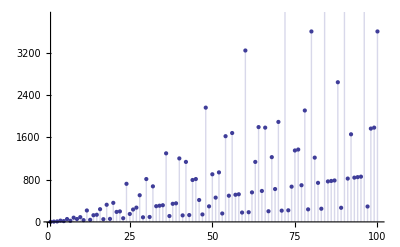

```mathematica
DiscretePlot[E1a[n,3,1.00000001,-1],{n,1,100}]
```

```mathematica
E2D2[100,3,1.1,0]
```

324.

```mathematica
D2a[100,3,0]
```

324

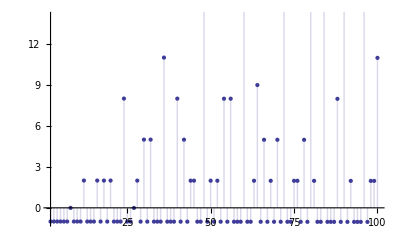

```mathematica
DiscretePlot[E2a[n,3,1.0001,0],{n,2,100}]
```

```mathematica
DiscretePlot[D2E2[n,3,1.0001,0],{n,2,100}]
```

-Graphics-

```mathematica
LinE[100,2,0]
```

4/5

```mathematica
E2a[100,1,101,0]
```

99

```mathematica
D[Expand[E1b[100,z,1.5,0]],z]/.z->0
```

-3.44534